### data reading

```mathematica
p0s={3.80,3.825,3.85}
```

{3.8,3.825,3.85}

```mathematica
temperatures={{0.063, 0.039, 0.03105 ,0.025, 0.016, 0.01 ,0.008, 0.0063 ,0.005, 0.00385 ,0.0031 , 0.0028 ,0.0025 ,0.0022},{0.063,0.039, 0.03105, 0.016 ,0.01, 0.008, 0.0063, 0.005 ,0.00385, 0.0031, 0.0025, 0.002, 0.0015,0.001, 0.00067 ,0.0005},{0.039, 0.016 ,0.01 ,0.005, 0.00385 ,0.0025, 0.002, 0.001, 0.0005, 0.00033, 0.00025 ,0.00014 ,0.000091, 0.000077,0.000054, 0.000045 ,0.000036}};
 records={{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19}};
tauEstimate={{1, 3, 4,8, 15, 40,70,150, 250, 600,2000 ,2500,4500,9500},{1, 2, 4 ,9 ,15,25, 40 ,60, 80, 120,200 ,300 ,1000 ,1500, 5000,10000},{2 ,4,10, 20, 40,60, 80,200, 500 ,800 ,1400, 2500 ,4200 ,5000, 6000,8500, 9500}};
(*tauEstimate={{1., 2., 4. ,9. ,15. ,25., 40. ,60., 80., 120. ,200. ,300. ,1000. ,1500., 5000. ,10000.},{1., 3., 4. ,8. ,15. ,40. ,70. ,150. ,250., 600. ,2000., 2500. ,4500., 9500.},{4. ,5. ,7. ,10. ,30. ,70., 150. ,700. ,1400., 4000. ,9500.}};*)
```

```mathematica
SACfitting={{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}};
```

```mathematica
tauAlphaCRSISF={{1.13.,2.12.,3.7.,5.24.,11.02.2,34.6.,58.10.,113.11.,234.7.,586.14.,1595.24.,2672.20.,4596.20.,8808.36.},{1.24.,2.4.,3.22.8,9.01.5,18.51.6,27.5.,41.5.,56.4.,95.5.,136.6.,227.11.,303.8.,563.9.,1171.15.,4893.45.,13252.74.},{1.42.6,4.71.5,8.91.7,20.91.5,28.01.5,48.4.,74.63.0,193.4.,557.10.,1213.42.,1624.29.,4184.45.,10376.187.,11687.237.,25941.343.,31903.490.,44031.615.}}
```

{{1.13.,2.12.,3.7.,5.24.,11.02.2,34.6.,58.10.,113.11.,234.7.,586.14.,1595.24.,2672.20.,4596.20.,8808.36.},{1.24.,2.4.,3.22.8,9.01.5,18.51.6,27.5.,41.5.,56.4.,95.5.,136.6.,227.11.,303.8.,563.9.,1171.15.,4893.45.,13252.74.},{1.42.6,4.71.5,8.91.7,20.91.5,28.01.5,48.4.,74.63.0,193.4.,557.10.,1213.42.,1624.29.,4184.45.,10376.187.,11687.237.,25941.343.,31903.490.,44031.615.}}

```mathematica
tauCRoverlap={{5.833319418117253,11.86278894161065,16.917338892978847,23.25548620200179,52.160702899712064,144.03673884723923,226.53383746332744,388.1550799983505,724.5750497347012,1566.498812260033,3781.0544591126413,5197.718904387892,9467.910598016313,16829.017670811918},{4.908732268246582,9.31848873794692,13.186591725727347,32.26259187830922,66.35481014996512,100.38226732553892,143.960577154809,209.23274864109732,333.8968037849868,460.04501744315485,668.6308529783303,958.8992763643564,1725.6436531887025,4336.275018528646,13857.138919303605,33009.675825311846},{7.834976775992932,22.460497359787702,40.922793734483406,94.78280185436874,128.79453931137476,231.55461796962314,323.17926259327726,843.8681996277791,2586.1167985909237,5036.916402039757,7314.717671434624,18600.880936529808,40307.93498223004,52624.590535830495,98462.79050610549,139254.67185534368,202268.02162912188}};
```

```mathematica
tauG=Table[Table[Around[SACfitting[[p,T]]["BestFitParameters"][[2,2]],SACfitting[[p,T]]["ParameterErrors"][[2]]],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

FittedModel::constr: The property values {ParameterErrors} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::stop: Further output of FittedModel::constr will be suppressed during this calculation.

{{1.520.20,2.190.13,2.80.4,3.510.26,6.00.6,10.80.5,18.20.5,24.40.5,38.61.0,97.81.8,179.6.,327.4.,535.92.8,860.6.},{1.260.22,2.00.4,2.40.6,5.10.4,7.80.6,9.20.7,12.01.9,17.70.7,24.11.2,34.62.1,45.42.4,70.52.5,103.63.5,286.7.,835.14.,1328.20.},{1.630.33,3.81.3,5.41.0,11.71.2,15.02.1,25.51.6,32.02.8,81.7.,171.16.,271.26.,286.77.,384.115.,232.83.,347.161.,314.148.,1037.427.,340.221.}}

```mathematica
plateauG=Table[Table[Around[SACfitting[[p,T]]["BestFitParameters"][[1,2]],SACfitting[[p,T]]["ParameterErrors"][[1]]],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

FittedModel::constr: The property values {ParameterErrors} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::stop: Further output of FittedModel::constr will be suppressed during this calculation.

{{0.2090.026,0.2000.012,0.1830.028,0.1640.012,0.1370.013,0.1020.004,0.08540.0016,0.07120.0010,0.05860.0010,0.04820.0005,0.03510.0007,0.035060.00022,0.026820.00008,0.021890.00006},{0.210.04,0.170.04,0.150.04,0.1000.008,0.0780.005,0.0700.004,0.0560.007,0.04650.0015,0.03970.0015,0.03100.0013,0.02420.0009,0.02060.0005,0.014040.00031,0.010390.00015,0.006230.00006,0.0038640.000028},{0.160.04,0.0920.032,0.0700.012,0.03540.0033,0.02990.0032,0.01840.0009,0.01600.0012,0.00840.0006,0.004900.00034,0.003370.00023,0.00380.0004,0.003320.00032,0.002450.00033,0.002010.00032,0.001970.00033,0.001890.00023,0.00180.0004}}

```mathematica
betaG=Table[Table[Around[SACfitting[[p,T]]["BestFitParameters"][[3,2]],SACfitting[[p,T]]["ParameterErrors"][[3]]],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

FittedModel::constr: The property values {ParameterErrors} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::stop: Further output of FittedModel::constr will be suppressed during this calculation.

{{1.000.10,0.970.04,0.960.10,0.990.05,0.920.07,0.8300.030,0.8430.020,0.7830.016,0.7010.017,0.6710.014,0.6990.030,0.6790.010,0.6760.006,0.7010.006},{1.000.11,0.990.12,0.980.13,0.980.05,0.860.04,0.870.04,0.800.08,0.8540.025,0.8370.031,0.810.04,0.810.04,0.830.04,0.810.04,0.8120.035,0.8360.029,0.8130.021},{0.930.09,0.920.18,0.870.10,0.920.07,0.860.09,0.900.05,0.940.07,0.940.09,0.890.11,0.900.12,0.480.07,0.370.04,0.440.07,0.400.08,0.410.08,0.350.06,0.370.08}}

```mathematica
Length[betaG[[3]]]
```

17

```mathematica
tg={{0.003430184515278148,0.002155828227332618},{0.0011179088576272092,0.000542496243679735},{0.000367,0.0000866}};;(*T at which tau_Alpha =1000 or 10000*)
```

```mathematica
compressibility={{0.011199273784966107,0.006843271602432324,0.005611288719792794,0.005041234977461774,0.0034425583850431754,0.0026057510940828517,0.002402093767504809,0.0019966246441788602,0.0019182227717051852,0.0019049662456268918,0.001449880590064925,0.0013399825929035518,0.001187690840811528,0.001014343011690452},{0.010973863616378617,0.006969729232530318,0.006019921555357807,0.0034470215575048853,0.0026329094381145244,0.0022131356244573337,0.0019444910237750798,0.0016014985435969943,0.0013760687245457778,0.001195880727373862,0.0010327648584341675,0.000874898354553366,0.0007622957395221339},{0.007453560814727081,0.0038553113302460763,0.0028135912408168745,0.0017419724263324672,0.0014223701929428829,0.0010685323178511355,0.0008038075411382475,0.00047302076751918546,0.0002508192704905529,0.00015879046536729807,0.0001292071964184393,0.00007178071005006233,0.00004788692408399204,0.00003644992471026816,0.000027944243002211488,0.000025979680020164673,0.00001885945885242752}};
```

## Gp

### fit G_p

```mathematica
fittingRange={{5,10},{5,12},{1,10}};
```

```mathematica
niceStretchedExpStartEnd={{1,14},{1,16},{1,10}};
```

```mathematica
Gpfits=Table[NonlinearModelFit[Table[{temperatures[[p,T]],plateauG[[p,T]]},{T,fittingRange[[p,1]],fittingRange[[p,2]]}],{A*x^B,{B<0.999}},{A,B},x],{p,Length[p0s]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[If[niceStretchedExp[[p,T]]==1,"ClosedMarkers","OpenMarkers"]
```

```mathematica
plateauSISFfits[[1,12,1]]
```

0.0328333

```mathematica
N[NumberForm[Gpfits[[3]]["BestFitParameters"][[2,2]],2]]
```

0.82

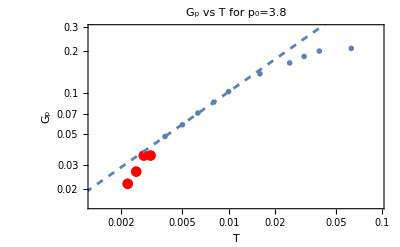
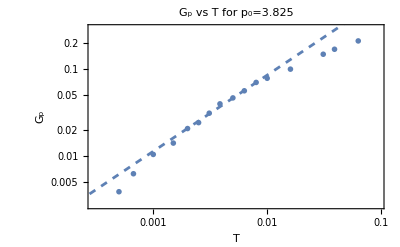
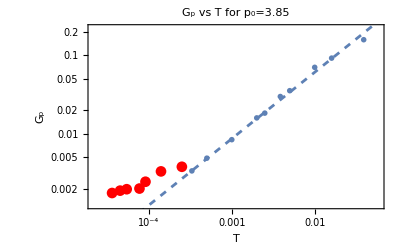

```mathematica
GpPlots=Table[Show[ListLogLogPlot[Table[{temperatures[[p,T]],plateauG[[p,T]][[1]]},{T,niceStretchedExpStartEnd[[p,1]]-1}],FrameLabel->{"T","G_p "},ImageSize->400,PlotMarkers->Automatic,PlotStyle->redBluePlotConfig[2][[1]],PlotLabel->"G_p vs T for p_0="<>ToString[p0s[[p]]],PlotRange->{{temperatures[[p,Length[temperatures[[p]]]]]*0.6,temperatures[[p,1]]*1.5},{plateauSISFfits[[p,Length[temperatures[[p]]]]][[1]]*0.7,Max[plateauSISFfits[[p,;;,1]]]*1.4}}],ListLogLogPlot[Table[{temperatures[[p,T]],plateauG[[p,T,1]]},{T,niceStretchedExpStartEnd[[p,1]],niceStretchedExpStartEnd[[p,2]]}],PlotLegends->"T^"<>ToString[NumberForm[Gpfits[[p]]["BestFitParameters"][[2,2]],2]],PlotMarkers->"OpenMarkers",FrameLabel->{"T","G_p "}],ListLogLogPlot[Table[{temperatures[[p,T]],plateauG[[p,T,1]]},{T,niceStretchedExpStartEnd[[p,2]]+1,Length[temperatures[[p]]]}],PlotMarkers->Automatic,PlotStyle->redBluePlotConfig[2][[1]],FrameLabel->{"T","G_p "}],LogLogPlot[Gpfits[[p]][T],{T,0.00001,0.1},PlotStyle->Dashed]],{p,1,3}]
```

```mathematica
Table[Table[{temperatures[[p,T]]/
tg[[p,1]],plateauG[[p,T,1]]},{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{{18.3664,0.209414},{11.3697,0.200228},{9.05199,0.183037},{7.28824,0.164365},{4.66447,0.137041},{2.9153,0.101834},{2.33224,0.0853956},{1.83664,0.0712389},{1.45765,0.0585905},{1.12239,0.0482334},{0.903741,0.0350755},{0.816283,0.0350585},{0.728824,0.0268177},{0.641365,0.0218948}},{{56.3552,0.210951},{34.8866,0.169126},{27.7751,0.148186},{14.3124,0.0997807},{8.94527,0.0783462},{7.15622,0.0701678},{5.63552,0.0561925},{4.47264,0.0465456},{3.44393,0.0397446},{2.77303,0.0310282},{2.23632,0.0241522},{1.78905,0.0206433},{1.34179,0.0140389},{0.894527,0.0103928},{0.599333,0.00622658},{0.447264,0.00386398}},{{106.267,0.15809},{43.5967,0.0921263},{27.248,0.0703362},{13.624,0.0354478},{10.4905,0.0298741},{6.81199,0.0183639},{5.44959,0.0159577},{2.7248,0.00842671},{1.3624,0.00489603},{0.899183,0.00337131},{0.681199,0.00380535},{0.381471,0.00332378},{0.247956,0.00245389},{0.209809,0.00200915},{0.147139,0.0019701},{0.122616,0.00189001},{0.0980926,0.00176269}}}

```mathematica
$UserBaseDirectory
```

/home/chengling/.Mathematica

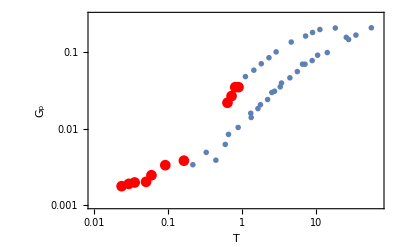

```mathematica
Show[Table[ListLogLogPlot[Table[{temperatures[[p,T]]/
tg[[p,1]],plateauG[[p,T,1]]},{T,niceStretchedExpStartEnd[[p,1]],niceStretchedExpStartEnd[[p,2]]}],PlotMarkers->"OpenMarkers",FrameLabel->{"T","G_p "},PlotRange->{{0.01,70},{0.001,0.3}}],{p,1,3}],Table[ListLogLogPlot[Table[{temperatures[[p,T]]/
tg[[p,1]],plateauG[[p,T,1]]},{T,niceStretchedExpStartEnd[[p,2]]+1,Length[temperatures[[p]]]}],PlotMarkers->Automatic,PlotStyle->redBluePlotConfig[2][[1]],FrameLabel->{"T","G_p "}],{p,1,3}]]
```

```mathematica
Length[temperatures[[2]]]
```

16

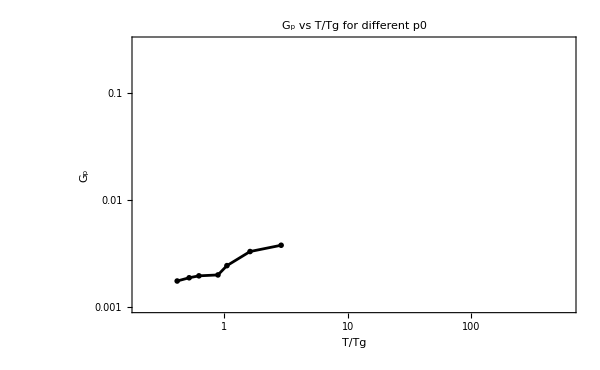

PlotMarkers→Automatic

```mathematica
ListLogLogPlot[Table[Table[{temperatures[[p,T]]/
tg[[p,2]],plateauG[[p,T,1]]},{T,niceStretchedExpStartEnd[[p,2]]+1,Length[temperatures[[p]]]}],{p,3,3}],PlotMarkers->"OpenMarkers",FrameLabel->{"T/Tg","G_p"},PlotStyle->gradientColScheme[5],PlotRange->{{0.21,600},{0.001,0.3}},Joined->True,ImageSize->600,PlotLabel->"G_p vs T/Tg for different p0"]
```

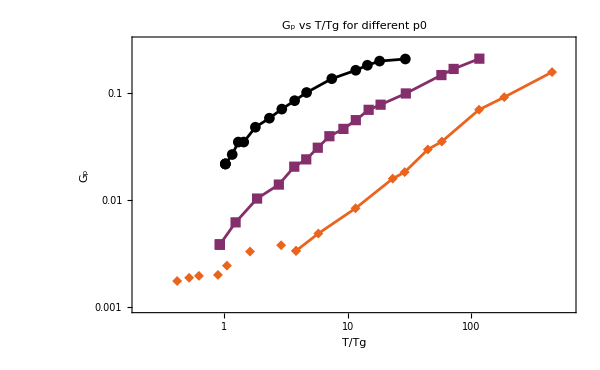

```mathematica
gpPlot=Show[ListLogLogPlot[Table[Table[{temperatures[[p,T]]/
tg[[p,2]],plateauG[[p,T,1]]},{T,niceStretchedExpStartEnd[[p,1]],niceStretchedExpStartEnd[[p,2]]}],{p,1,3}],PlotStyle->gradientColScheme[5],PlotMarkers->Automatic,FrameLabel->{"T/Tg","G_p"},PlotRange->{{0.21,600},{0.001,0.3}},Joined->True,ImageSize->600,PlotLabel->"G_p vs T/Tg for different p0"(*, PlotLegends->Table["p_0="<>ToString[p0s[[p]]],{p,3}]*)],ListLogLogPlot[Table[Table[{temperatures[[p,T]]/
tg[[p,2]],plateauG[[p,T,1]]},{T,niceStretchedExpStartEnd[[p,2]],Length[temperatures[[p]]]}],{p,1,3}],PlotStyle->gradientColScheme[5],PlotMarkers->Automatic,FrameLabel->{"Tg/T","G_p "}]]
```

```mathematica
Export["/home/chengling/Research/updates/07142024/gpPlot.jpeg",gpPlot,ImageResolution->400]
```

/home/chengling/Research/updates/07142024/gpPlot.jpeg

```mathematica
β
```

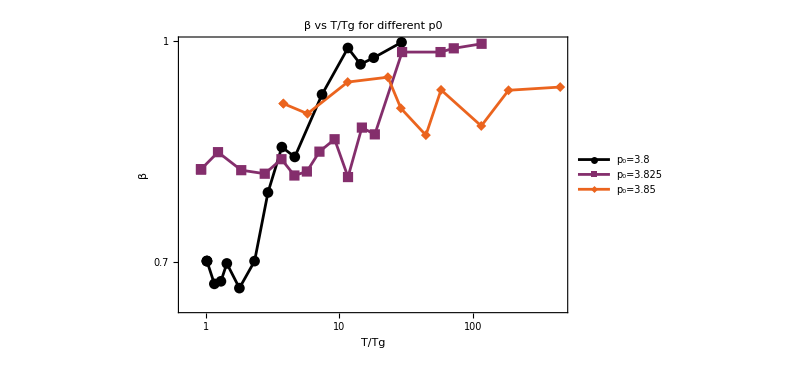

```mathematica
betaPLot=Show[ListLogLogPlot[Table[Table[{temperatures[[p,T]]/
tg[[p,2]],betaG[[p,T,1]]},{T,niceStretchedExpStartEnd[[p,1]],niceStretchedExpStartEnd[[p,2]]}],{p,1,3}],PlotStyle->gradientColScheme[5],PlotMarkers->Automatic,FrameLabel->{"T/Tg","β"},PlotRange->All,Joined->True,ImageSize->600,PlotLabel->"β vs T/Tg for different p0", PlotLegends->Table["p_0="<>ToString[p0s[[p]]],{p,3}]],ListLogLogPlot[Table[Table[{temperatures[[p,T]]/
tg[[p,2]],betaG[[p,T,1]]},{T,niceStretchedExpStartEnd[[p,2]],Length[temperatures[[p]]]}],{p,1,3}],PlotStyle->gradientColScheme[5],PlotMarkers->Automatic,FrameLabel->{"Tg/T","G_p "}]]
```

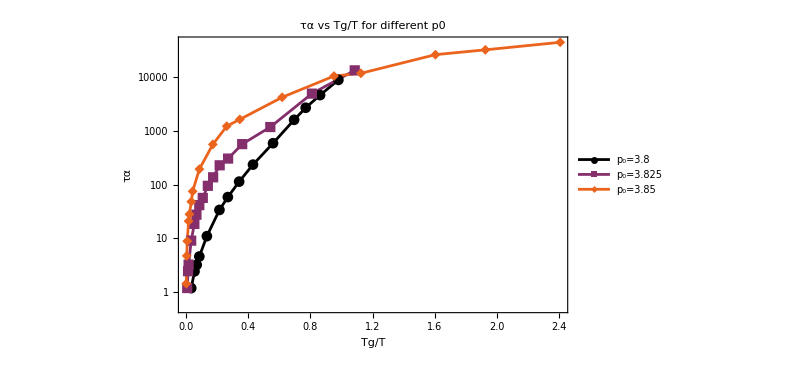

```mathematica
tauAlphaPlot=Show[ListLogPlot[Table[Table[{tg[[p,2]]/temperatures[[p,T]],tauAlphaCRSISF[[p,T,1]]},{T,Length[temperatures[[p]]]}],{p,1,3}],PlotStyle->gradientColScheme[5],PlotMarkers->Automatic,FrameLabel->{"Tg/T","τα"},PlotRange->All,Joined->True,ImageSize->600,PlotLabel->"τα vs Tg/T for different p0", PlotLegends->Table["p_0="<>ToString[p0s[[p]]],{p,3}]]]
```

```mathematica
Export["/home/chengling/Research/updates/07142024/betaPlot.jpeg",Grid[Partition[{gpPlot,betaPLot},2]],ImageResolution->400]
```

/home/chengling/Research/updates/07142024/betaPlot.jpeg

```mathematica
Export["/home/chengling/Research/updates/07142024/tauAlphaPlot.jpeg",tauAlphaPlot,ImageResolution->400]
```

/home/chengling/Research/updates/07142024/tauAlphaPlot.jpeg

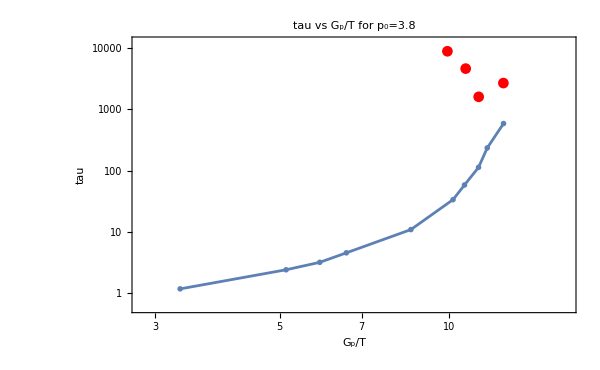
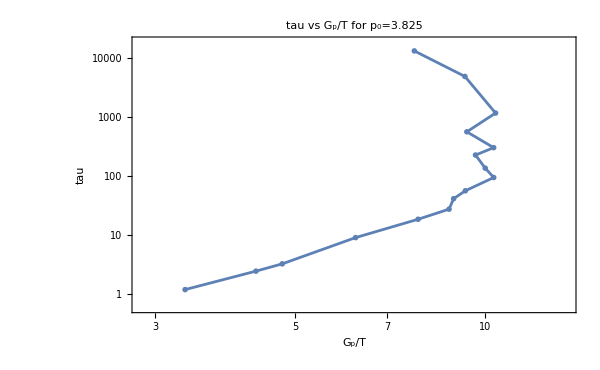
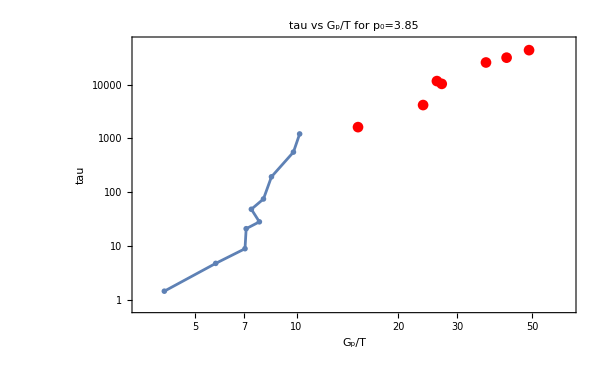

```mathematica
tauGpplots=Table[Show[ListLogLogPlot[Table[{plateauG[[p,T]][[1]]/temperatures[[p,T]],tauAlphaCRSISF[[p,T,1]]},{T,niceStretchedExpStartEnd[[p,1]]-1}],FrameLabel->{"G_p/T ","tau"},ImageSize->600,PlotMarkers->Automatic,PlotStyle->redBluePlotConfig[2][[1]],PlotLabel->"tau vs G_p/T for p_0="<>ToString[p0s[[p]]],PlotRange->{{Min[plateauG[[p,;;,1]]/temperatures[[p,;;]]]*0.85,Max[plateauG[[p,;;,1]]/temperatures[[p,;;]]]*1.3},{Min[tauAlphaCRSISF[[p,;;,1]]]*0.5,Max[tauAlphaCRSISF[[p,;;,1]]]*1.4}}],ListLogLogPlot[Table[{plateauG[[p,T]][[1]]/temperatures[[p,T]],tauAlphaCRSISF[[p,T,1]]},{T,niceStretchedExpStartEnd[[p,1]],niceStretchedExpStartEnd[[p,2]]}],Joined->True,PlotMarkers->"OpenMarkers",FrameLabel->{"T","G_p/T "}],ListLogLogPlot[Table[{plateauG[[p,T]][[1]]/temperatures[[p,T]],tauAlphaCRSISF[[p,T,1]]},{T,niceStretchedExpStartEnd[[p,2]]+1,Length[temperatures[[p]]]}],PlotMarkers->Automatic,PlotStyle->redBluePlotConfig[2][[1]],FrameLabel->{"T","G_p "}],LogLogPlot[Gpfits[[p]][T],{T,0.00001,0.1},PlotStyle->Dashed]],{p,Length[p0s]}]
```

```mathematica
edgeLenghts={{0.00027275898477512175,0.0004721126535879246,0.00044454023439870275,0.00043817111805756785,0.0006566831654090658,0.0009721808477960356,0.0011618812738573064,0.0013578120802668861,0.0017769091670504283,0.001691276952055129,0.0023199396384411862,0.00252059214991496,0.0043444796174066614,0.003512506268562504},{0.00028152150173489275,0.00038073141603911097,0.000318410555840788,0.0005803711148173594,0.0006302710613325824,0.0008193903773189931,0.000827064018368142,0.0007631414454449609,0.0010090272879310928,0.0011747117413946544,0.0012760169230994732,0.0010334186664275435,0.0014628895006426018,0.0023120024660016002,0.0028159345528204144,0.0027950380876794892},{0.0003614940589666243,0.00040605450028656905,0.0004663536889932632,0.0005298627531469939,0.0007678665779848077,0.0008005807875595058,0.0009523699575691595,0.0012048228653113553,0.0012891630221554915,0.0010929724342149325,0.0013494921623228948,0.0016210383629023536,0.001353098310772653,0.001792949329997795,0.001761012250781124,0.0018129381144339509,0.001577367410273238}};
```

```mathematica
gpPerimeter={{0.1650.019,0.180.04,0.1510.017,0.1370.007,0.1270.016,0.09280.0029,0.07340.0015,0.06180.0013,0.04230.0010,0.03280.0007,0.025400.00018,0.018070.00014,0.017940.00011,0.012780.00009},{0.180.04,0.120.04,0.110.07,0.1080.032,0.0650.010,0.0590.007,0.04250.0028,0.0420.004,0.02810.0024,0.02070.0020,0.01850.0010,0.01300.0008,0.00930.0008,0.005350.00027,0.001860.00013,0.000900.00008},{0.180.32,0.080.04,0.0520.018,0.0380.007,0.0300.007,0.01310.0028,0.00830.0023,0.0180.021,0.0040.004,0.00280.0007,0.0060.004,0.00420.0010,0.00400.0007,0.00450.0014,0.00340.0006,0.002280.00025,0.00290.0004}};
```

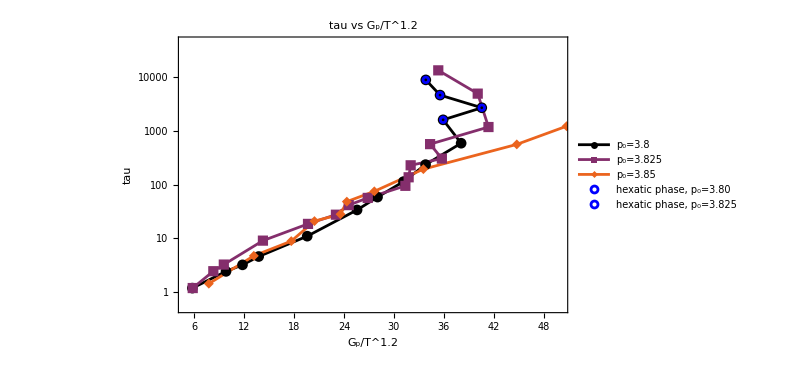

```mathematica
update0714=Show[ListLogPlot[Table[Table[{plateauG[[p,T]][[1]]/temperatures[[p,T]]^1.2,tauAlphaCRSISF[[p,T,1]]},{T,Length[temperatures[[p]]]}],{p,3}],PlotStyle->gradientColScheme[5],FrameLabel->{"G_p/T^1.2 ","tau"},ImageSize->600,PlotMarkers->Automatic,PlotStyle->redBluePlotConfig[2][[1]],PlotLabel->"tau vs G_p/T^1.2",PlotLegends->Table["p_0="<>ToString[p0s[[p]]],{p,Length[p0s]}],PlotRange->{{5,50},All},Joined->True],ListLogPlot[Table[Table[{plateauG[[p,T]][[1]]/temperatures[[p,T]]^1.2,tauAlphaCRSISF[[p,T,1]]},{T,Length[temperatures[[p]]]-{3,1}[[p]],Length[temperatures[[p]]]}],{p,2}],FrameLabel->{"G_p/T ","tau"},ImageSize->600,PlotMarkers->{Graphics[{Blue,Circle[]}],0.05},PlotStyle->redBluePlotConfig[2][[1]],PlotLabel->"tau vs G_p/T",PlotLegends->{"hexatic phase, p_0=3.80","hexatic phase, p_0=3.825"},PlotRange->{{2,14},All},Joined->False]]
```

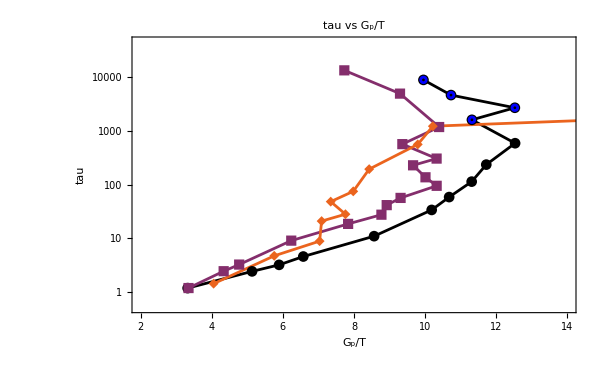

```mathematica
update0715=Show[ListLogPlot[Table[Table[{plateauG[[p,T]][[1]]/temperatures[[p,T]],tauAlphaCRSISF[[p,T,1]]},{T,Length[temperatures[[p]]]}],{p,3}],PlotStyle->gradientColScheme[5],FrameLabel->{"G_p/T ","tau"},ImageSize->600,PlotMarkers->Automatic,PlotStyle->redBluePlotConfig[2][[1]],PlotLabel->"tau vs G_p/T"(*,PlotLegends->Table["p_0="<>ToString[p0s[[p]]],{p,Length[p0s]}]*),PlotRange->{{2,14},All},Joined->True],ListLogPlot[Table[Table[{plateauG[[p,T]][[1]]/temperatures[[p,T]],tauAlphaCRSISF[[p,T,1]]},{T,Length[temperatures[[p]]]-{3,1}[[p]],Length[temperatures[[p]]]}],{p,2}],FrameLabel->{"G_p/T ","tau"},ImageSize->600,PlotMarkers->{Graphics[{Blue,Circle[]}],0.05},PlotStyle->redBluePlotConfig[2][[1]],PlotLabel->"tau vs G_p/T"(*,PlotLegends->{"hexatic phase, p_0=3.80","hexatic phase, p_0=3.825"}*),PlotRange->{{2,14},All},Joined->False]]
```

```mathematica
Export["/home/chengling/Research/updates/07142024/gpscaleT.jpeg",Grid[Partition[{update0715,update0714},2]],ImageResolution->400]
```

/home/chengling/Research/updates/07142024/gpscaleT.jpeg

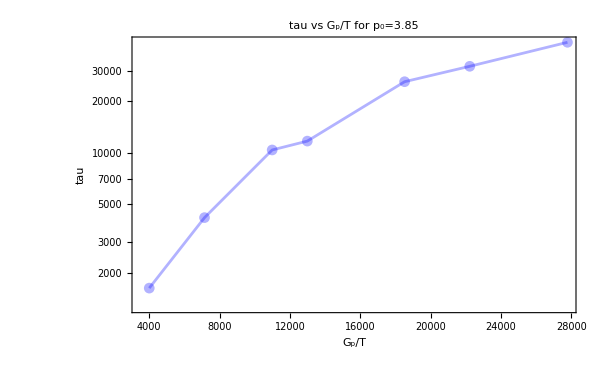

```mathematica
gptPlot=Show[Table[ListLogPlot[Table[{1/temperatures[[p,T]]^(1),tauAlphaCRSISF[[p,T,1]]},{T,niceStretchedExpStartEnd[[p,2]]+1,Length[temperatures[[p]]]}],PlotStyle->redBluePlotConfig[3][[p]],FrameLabel->{"G_p/T ","tau"},ImageSize->600,PlotMarkers->Automatic,PlotStyle->redBluePlotConfig[2][[1]],PlotLabel->"tau vs G_p/T for p_0="<>ToString[p0s[[p]]],PlotRange->All,Joined->True],{p,3,3}]]
```

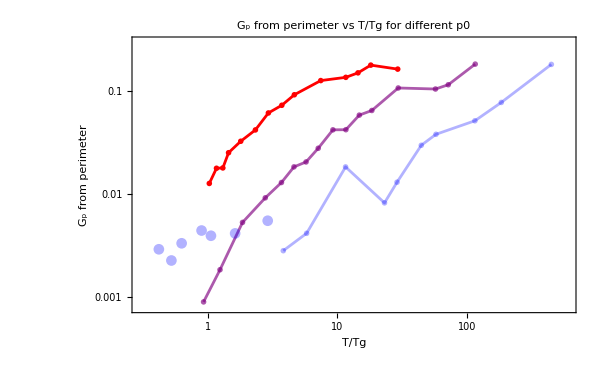

```mathematica
gpPlotPerimeterPlot=Show[Table[ListLogLogPlot[Table[{temperatures[[p,T]]/
tg[[p,2]],gpPerimeter[[p,T,1]]},{T,niceStretchedExpStartEnd[[p,1]],niceStretchedExpStartEnd[[p,2]]}],PlotMarkers->"OpenMarkers",FrameLabel->{"T/Tg","G_p from perimeter"},PlotStyle->redBluePlotConfig[3][[p]],PlotRange->{{0.3,600},{0.0008,0.3}},Joined->True,ImageSize->600,PlotLabel->"G_p from perimeter vs T/Tg for different p0"],{p,1,3}],Table[ListLogLogPlot[Table[{temperatures[[p,T]]/
tg[[p,2]],gpPerimeter[[p,T,1]]},{T,niceStretchedExpStartEnd[[p,2]]+1,Length[temperatures[[p]]]}],PlotMarkers->Automatic,PlotStyle->redBluePlotConfig[3][[p]],FrameLabel->{"Tg/T","G_p "}],{p,1,3}]]
```

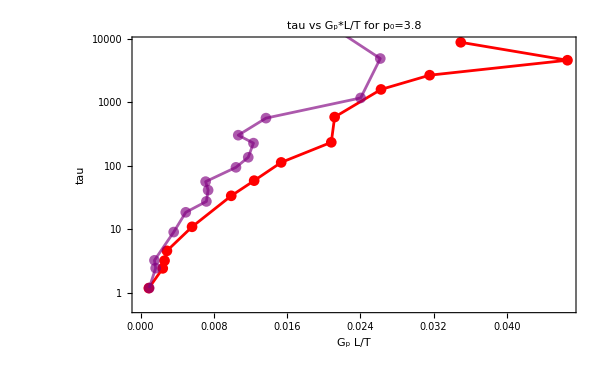

```mathematica
gpTLPlot=Show[Table[ListLogPlot[Table[{plateauG[[p,T]][[1]]*edgeLenghts[[p,T]]/temperatures[[p,T]],tauAlphaCRSISF[[p,T,1]]},{T,Length[temperatures[[p]]]}],PlotStyle->redBluePlotConfig[3][[p]],FrameLabel->{"G_p L/T ","tau"},ImageSize->600,PlotMarkers->Automatic,PlotStyle->redBluePlotConfig[2][[1]],PlotLabel->"tau vs G_p*L/T for p_0="<>ToString[p0s[[p]]],PlotRange->All,Joined->True],{p,1,2}]]
```

```mathematica
Export["/home/chengling/Research/updates/07072024/gpTplot.jpeg",Grid[Partition[{gptPlot,gpTLPlot},2]],ImageResolution->400]
```

/home/chengling/Research/updates/07072024/gpTplot.jpeg

```mathematica
Export["/home/chengling/Research/updates/07072024/gpPlot.jpeg",Grid[Partition[{gpPlot,gpPlotPerimeterPlot},2]],ImageResolution->400]
```

/home/chengling/Research/updates/07072024/gpPlot.jpeg

Part::partw: Part 14 of {0.0109739,0.00696973,0.00601992,0.00344702,0.00263291,0.00221314,0.00194449,0.0016015,0.00137607,0.00119588,«3»} does not exist.

Part::partw: Part 15 of {0.0109739,0.00696973,0.00601992,0.00344702,0.00263291,0.00221314,0.00194449,0.0016015,0.00137607,0.00119588,«3»} does not exist.

Part::partw: Part 16 of {0.0109739,0.00696973,0.00601992,0.00344702,0.00263291,0.00221314,0.00194449,0.0016015,0.00137607,0.00119588,«3»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

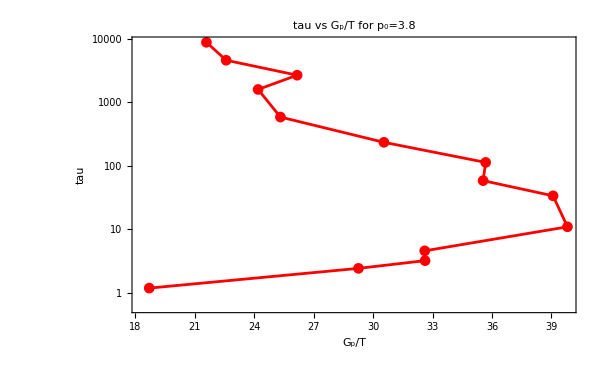
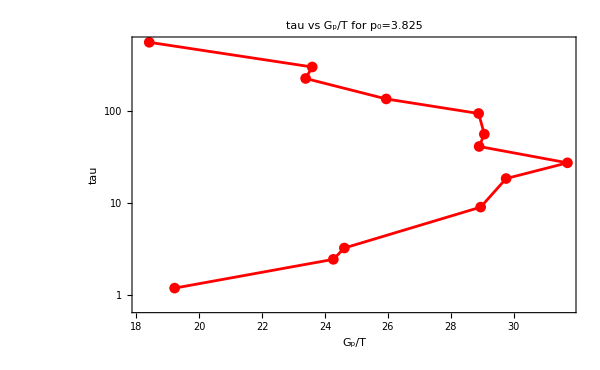
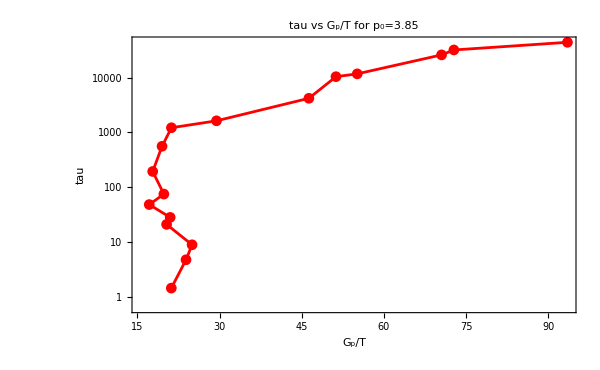

```mathematica
Table[Show[ListLogPlot[Table[{(plateauG[[p,T]][[1]]*(1)/(compressibility[[p,T]]/temperatures[[p,T]]))/temperatures[[p,T]],tauAlphaCRSISF[[p,T,1]]},{T,Length[temperatures[[p]]]}],FrameLabel->{"G_p/T ","tau"},ImageSize->600,PlotMarkers->Automatic,PlotStyle->redBluePlotConfig[2][[1]],PlotLabel->"tau vs G_p/T for p_0="<>ToString[p0s[[p]]],PlotRange->All,Joined->True]],{p,3}]
```

### connection with dynamics

```mathematica
tauAlphaNiceStretchedExpStartEnd={{1,8},{1,14},{2,10}};
```

```mathematica
tauAlphaCRSISF[[1,1,1]]
```

1.18553

```mathematica
taufitSISF=Table[NonlinearModelFit[Table[{1/temperatures[[p,T]],tauAlphaCRSISF[[p,T,1]]},{T,tauAlphaNiceStretchedExpStartEnd[[p,1]],tauAlphaNiceStretchedExpStartEnd[[p,2]]}],{A Exp[B t^(1-Gpfits[[p]]["BestFitParameters"][[2,2]])]},{A,B},t,MaxIterations->10000],{p,Length[p0s]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
taufitSISF=Table[NonlinearModelFit[Table[{1/temperatures[[p,T]],tauAlphaCRSISF[[p,T,1]]},{T,tauAlphaNiceStretchedExpStartEnd[[p,1]],tauAlphaNiceStretchedExpStartEnd[[p,2]]}],{A Exp[t^(1-Gpfits[[p]]["BestFitParameters"][[2,2]])]},{A},t,MaxIterations->10000,Method->{"NMinimize","RandomSeed"->1000}],{p,Length[p0s]}]
```

NonlinearModelFit::lmnl: The model A ⅇ^(t^0.338877) is linear in the parameters {A}, but a nonlinear method or non-Euclidean norm was specified, so nonlinear methods will be used.

NonlinearModelFit::lmnl: The model A ⅇ^(t^0.350886) is linear in the parameters {A}, but a nonlinear method or non-Euclidean norm was specified, so nonlinear methods will be used.

NonlinearModelFit::lmnl: The model A ⅇ^(t^0.153342) is linear in the parameters {A}, but a nonlinear method or non-Euclidean norm was specified, so nonlinear methods will be used.

General::stop: Further output of NonlinearModelFit::lmnl will be suppressed during this calculation.

{FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[NonlinearModelFit[Table[{1/temperatures[[p,T]],tauAlphaCRSISF[[p,T,1]]},{T,tauAlphaNiceStretchedExpStartEnd[[p,1]],tauAlphaNiceStretchedExpStartEnd[[p,2]]}],{A Exp[B t^(1-Gpfits[[p]]["BestFitParameters"][[2,2]])]},{B,A},t,MaxIterations->10000],{p,1,1}]
```

{FittedModel[…]}

```mathematica
Simplify[Log[a b^0.5]]
```

Log[a b^0.5]

```mathematica
taufit[[1]]
```

Part::partd: Part specification taufit⟦1⟧ is longer than depth of object.

taufit⟦1⟧

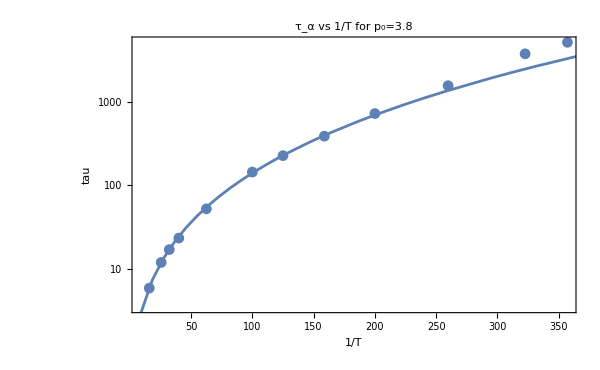

```mathematica
tauAlphaNiceStretchedExpStartEnd={{2,10},{1,14},{2,10}};
```

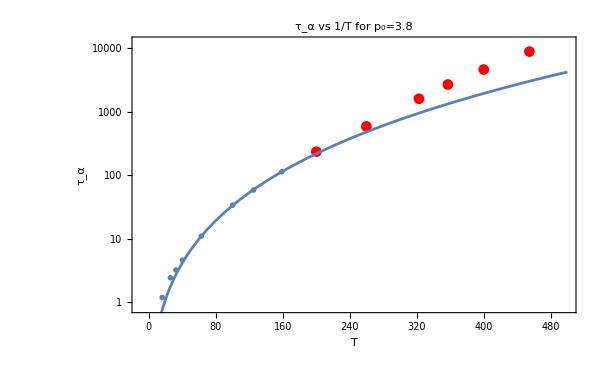
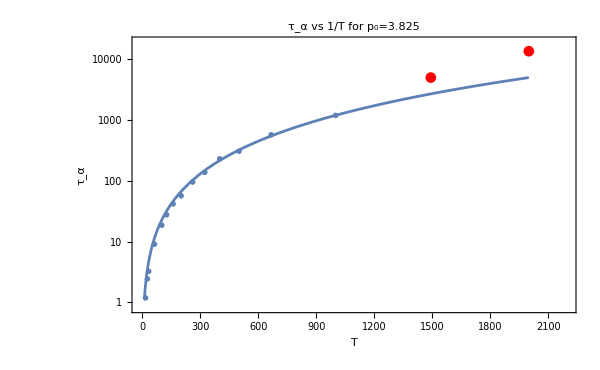
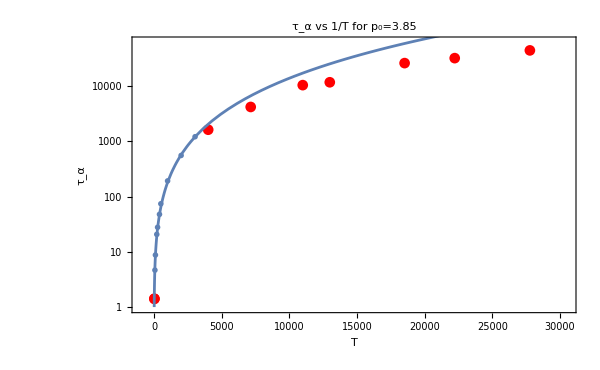

```mathematica
taufitPlots=Table[Show[ListLogPlot[Table[{1/temperatures[[p,T]],tauAlphaCRSISF[[p,T]][[1]]},{T,tauAlphaNiceStretchedExpStartEnd[[p,1]]-1}],FrameLabel->{"T","τ_α "},ImageSize->600,PlotMarkers->Automatic,PlotStyle->redBluePlotConfig[2][[1]],PlotLabel->"τ_α vs 1/T for p_0="<>ToString[p0s[[p]]],PlotRange->{{{-10,-10,-1000}[[p]],1/temperatures[[p,Length[temperatures[[p]]]]]*1.1},{tauAlphaCRSISF[[p,1]][[1]]*0.7,tauAlphaCRSISF[[p,Length[temperatures[[p]]],1]]*1.4}}],ListLogPlot[Table[{1/temperatures[[p,T]],tauAlphaCRSISF[[p,T,1]]},{T,tauAlphaNiceStretchedExpStartEnd[[p,1]],tauAlphaNiceStretchedExpStartEnd[[p,2]]}],PlotMarkers->"OpenMarkers",FrameLabel->{"T","G_p "}],ListLogPlot[Table[{1/temperatures[[p,T]],tauAlphaCRSISF[[p,T,1]]},{T,tauAlphaNiceStretchedExpStartEnd[[p,2]]+1,Length[temperatures[[p]]]}],PlotMarkers->Automatic,PlotStyle->redBluePlotConfig[2][[1]],FrameLabel->{"T","G_p "}],LogPlot[taufitSISF[[p]][t],{t,10,{500,2000,30000}[[p]]}]],{p,Length[p0s]}]
```

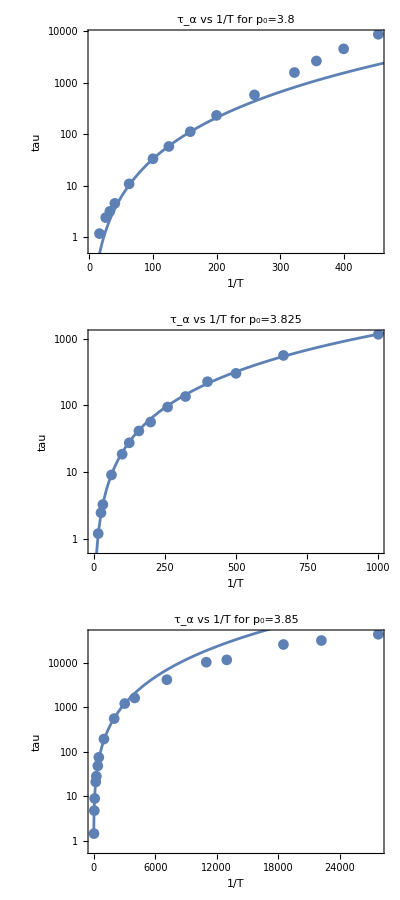

```mathematica
taufitPlots=Table[Show[ListLogPlot[Table[{1/temperatures[[p,T]],tauAlphaCRSISF[[p,T,1]]},{T,Length[temperatures[[p]]]}],FrameLabel->{"1/T","tau "},ImageSize->600,PlotLabel->"τ_α vs 1/T for p_0="<>ToString[p0s[[p]]],PlotRange->All(*PlotLegends->"Exp[T^-"<>ToString[NumberForm[1-Gpfits[[p,2]]["BestFitParameters"][[2,2]],2]]<>"]"*)],LogPlot[taufitSISF[[p]][t],{t,10,{500,1200,30000}[[p]]}]],{p,1,3}];
Column[taufitPlots]
```

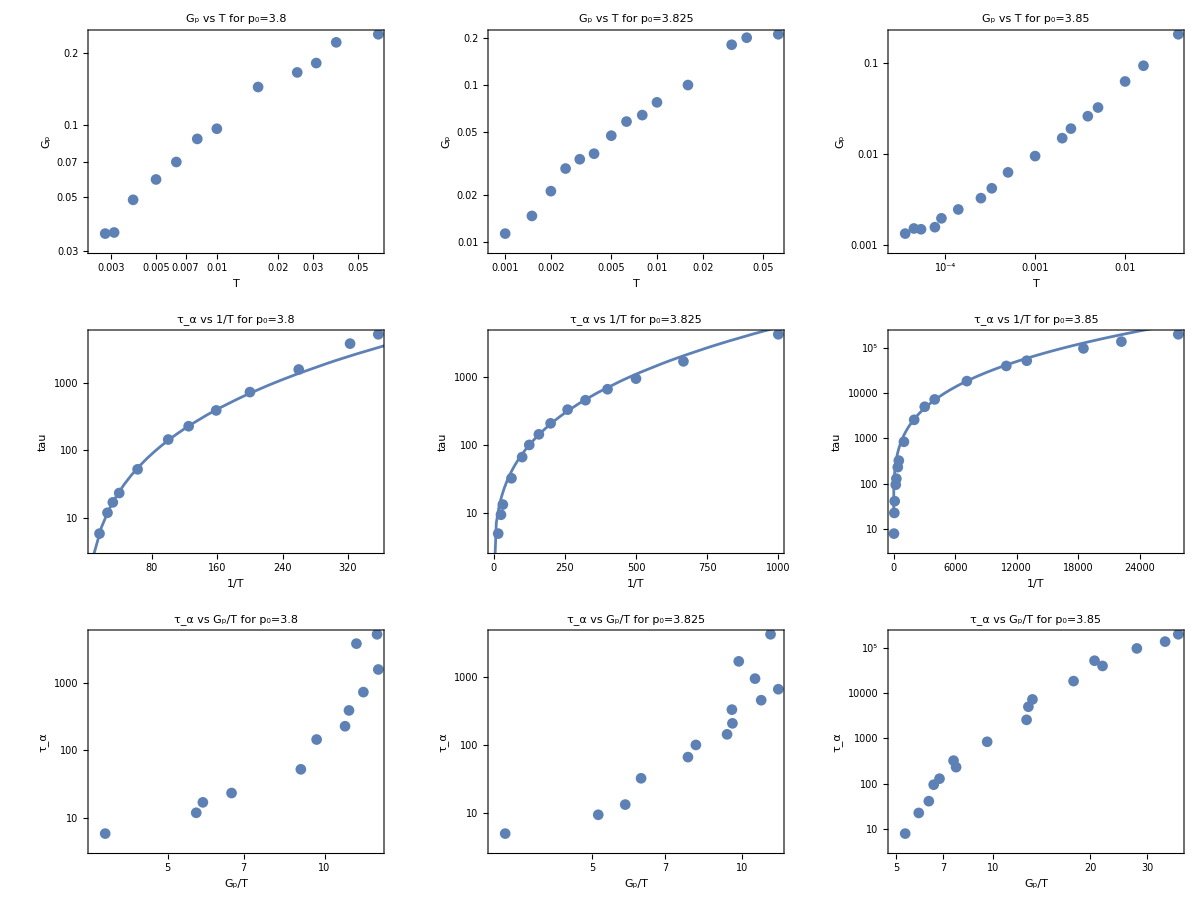

```mathematica
results=Grid[Partition[Flatten[{GPlots,taufitPlots,tauGpplots}],3]]
```

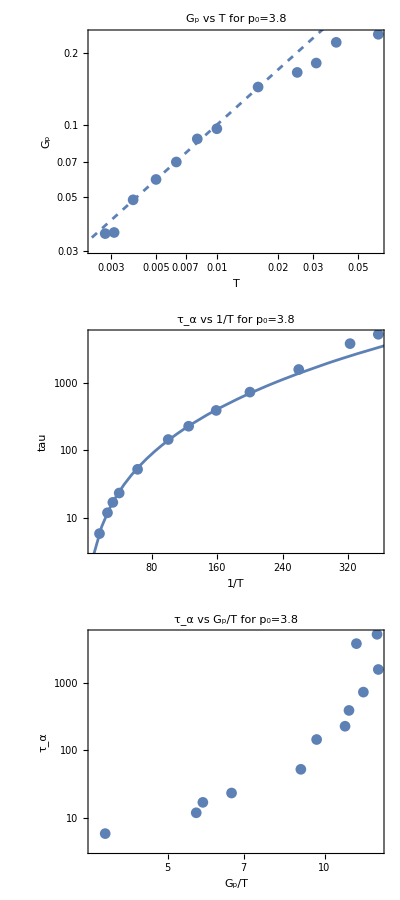

```mathematica
Column[{GPlots[[1]],taufitPlots[[1]],tauGpplots[[1]]}]
```

```mathematica
Table[Export["/home/chengling/Research/updates/05312024/Gpresults"<>ToString[p0s[[p]]]<>".jpeg",Column[{GPlots[[p]],taufitPlots[[p]],tauGpplots[[p]]}],ImageResolution->800],{p,Length[p0s]}]
```

{/home/chengling/Research/updates/05312024/Gpresults3.8.jpeg,/home/chengling/Research/updates/05312024/Gpresults3.825.jpeg,/home/chengling/Research/updates/05312024/Gpresults3.85.jpeg}

```mathematica
Export["/home/chengling/Research/updates/05312024/TauPLots.jpeg",Column[Table[Show[ListLogLogPlot[{Table[{temperatures[[p,T]],tauAlphaCRSISF[[p,T]]},{T,Length[temperatures[[p]]]}],Table[{temperatures[[p,T]],tauCRoverlap[[p,T]]},{T,Length[temperatures[[p]]]}],Table[{temperatures[[p,T]],tauG[[p,T]]},{T,Length[temperatures[[p]]]}]},FrameLabel->{"1/T","tau "},ImageSize->600,PlotLegends->{"CRSISF","CRoverlap","tau_G"},PlotLabel->"τ_α vs 1/T for p_0="<>ToString[p0s[[p]]],PlotRange->All(*PlotLegends->"Exp[T^-"<>ToString[NumberForm[1-Gpfits[[p,2]]["BestFitParameters"][[2,2]],2]]<>"]"*)]],{p,1,3}]],ImageResolution->800]
```

/home/chengling/Research/updates/05312024/TauPLots.jpeg

## tauAlpha

```mathematica
tauG[[;;,;;,1]]
```

{{1.51817,2.02293,2.87152,3.45734,5.00091,10.9347,18.2796,25.3105,44.372,118.762,196.127,349.152},{1.26016,1.99363,2.40251,5.11629,6.79964,8.83772,11.2576,17.7547,25.6143,34.7176,45.3932,71.1069,90.0039,282.602},{1.49628,3.21946,5.35835,11.8582,16.0978,23.6207,30.8218,70.6446,160.5,220.531,390.16,1489.15,339.173,588.301,513.034,1914.79,550.834}}

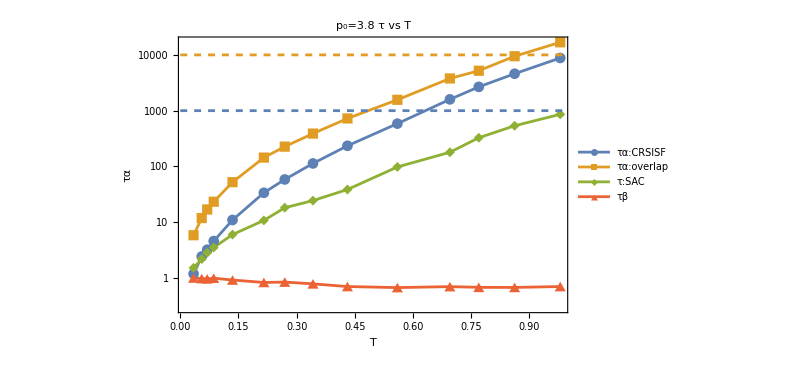
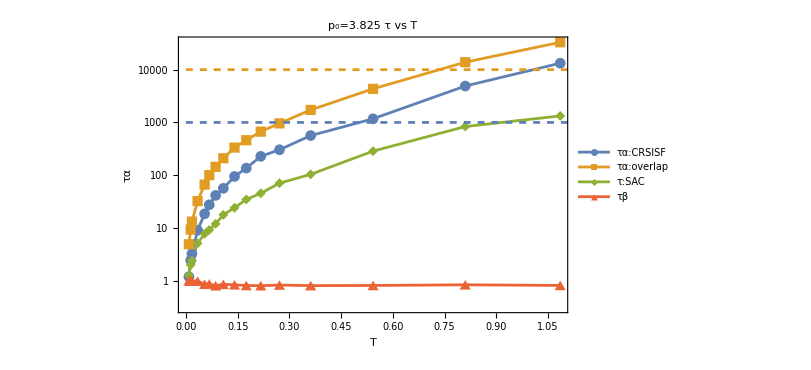
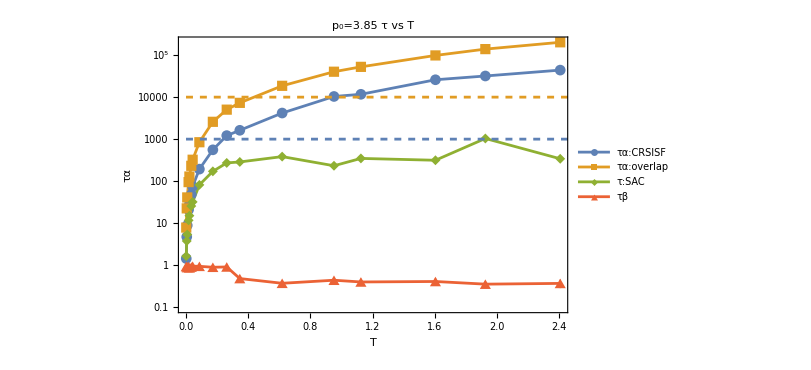

```mathematica
tauPlot=Table[Show[ListLogPlot[{Table[{tg[[p,2]]/temperatures[[p,T]],tauAlphaCRSISF[[p,T,1]]},{T,Length[temperatures[[p]]]}],Table[{tg[[p,2]]/temperatures[[p,T]],tauCRoverlap[[p,T]]},{T,Length[temperatures[[p]]]}],Table[{tg[[p,2]]/temperatures[[p,T]],tauG[[p,T,1]]},{T,Length[temperatures[[p]]]}],Table[{tg[[p,2]]/temperatures[[p,T]],betaG[[p,T]]},{T,Length[temperatures[[p]]]}]},FrameLabel->{"T","τα"},ImageSize->600,PlotMarkers->Automatic,PlotLabel->"p_0="<>ToString[p0s[[p]]]<>" τ vs T",Joined->True,PlotRange->All,PlotLegends->{"τα:CRSISF","τα:overlap","τ:SAC","τβ"}],LogPlot[{1000,10000},{x,0,{500,2000,35000}[[p]]},PlotStyle->{Dashed}]],{p,Length[p0s]}]
```

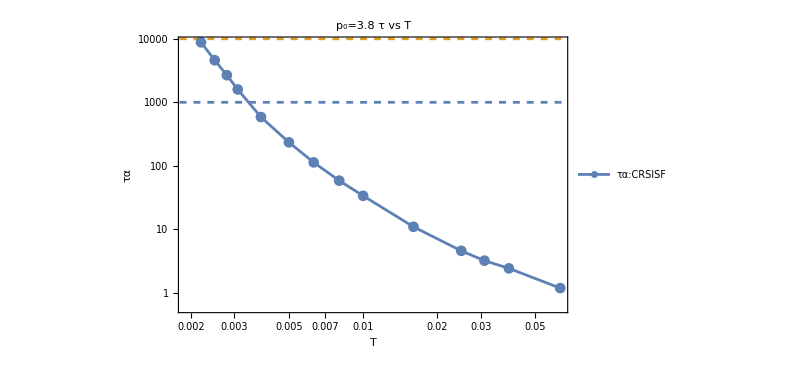
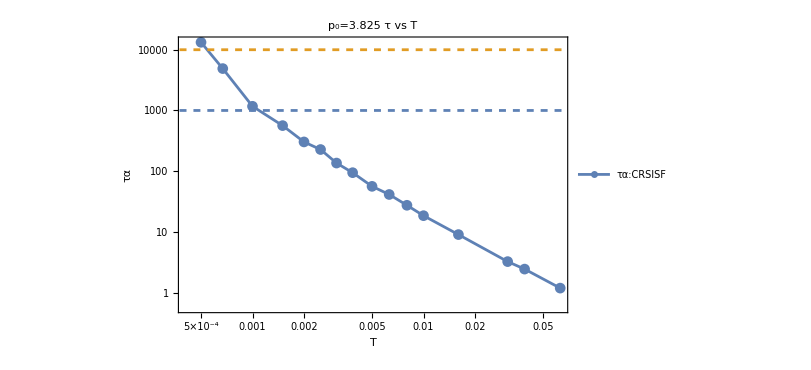
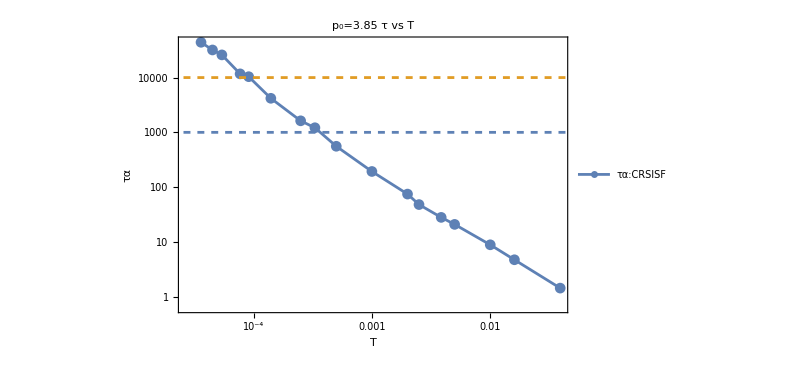

```mathematica
tauPlot=Table[Show[ListLogLogPlot[{Table[{temperatures[[p,T]],tauAlphaCRSISF[[p,T,1]]},{T,Length[temperatures[[p]]]}]},FrameLabel->{"T","τα"},ImageSize->600,PlotMarkers->Automatic,PlotLabel->"p_0="<>ToString[p0s[[p]]]<>" τ vs T",Joined->True,PlotRange->All,PlotLegends->{"τα:CRSISF","τα:overlap","τ:SAC","τβ"}],LogLogPlot[{1000,10000},{x,0.000001,0.5},PlotStyle->{Dashed}]],{p,Length[p0s]}]
```

```mathematica
tg={{0.003430184515278148,0.002155828227332618},{0.0011179088576272092,0.000542496243679735},{0.000367,0.0000866}};
```

```mathematica
Table[Export["/home/chengling/Research/updates/06242024/GpPlots"<>ToString[p0s[[p]]]<>".jpeg",GpPlots[[p]],ImageResolution->800],{p,Length[p0s]}]
```

{/home/chengling/Research/updates/06242024/GpPlots3.8.jpeg,/home/chengling/Research/updates/06242024/GpPlots3.825.jpeg,/home/chengling/Research/updates/06242024/GpPlots3.85.jpeg}

```mathematica
Table[Export["/home/chengling/Research/updates/06242024/tauGp"<>ToString[p0s[[p]]]<>".jpeg",tauGpplots[[p]],ImageResolution->800],{p,Length[p0s]}]
```

{/home/chengling/Research/updates/06242024/tauGp3.8.jpeg,/home/chengling/Research/updates/06242024/tauGp3.825.jpeg,/home/chengling/Research/updates/06242024/tauGp3.85.jpeg}

```mathematica
Table[Export["/home/chengling/Research/updates/06242024/tauFit"<>ToString[p0s[[p]]]<>".jpeg",taufitPlots[[p]],ImageResolution->800],{p,Length[p0s]}]
```

{/home/chengling/Research/updates/06242024/tauFit3.8.jpeg,/home/chengling/Research/updates/06242024/tauFit3.825.jpeg,/home/chengling/Research/updates/06242024/tauFit3.85.jpeg}

```mathematica
Table[Export["/home/chengling/Research/updates/06242024/taus"<>ToString[p0s[[p]]]<>".jpeg",tauPlot[[p]],ImageResolution->800],{p,Length[p0s]}]
```

{/home/chengling/Research/updates/06242024/taus3.8.jpeg,/home/chengling/Research/updates/06242024/taus3.825.jpeg,/home/chengling/Research/updates/06242024/taus3.85.jpeg}

## Bulk Modulus

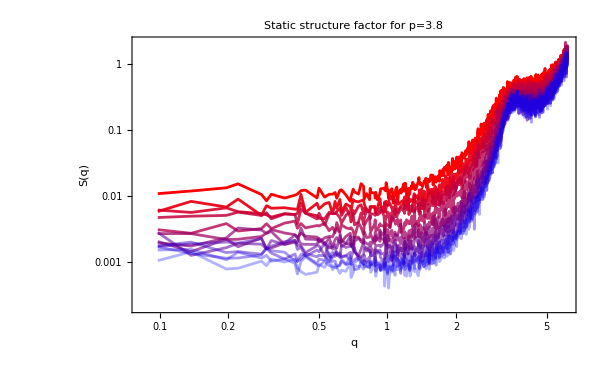
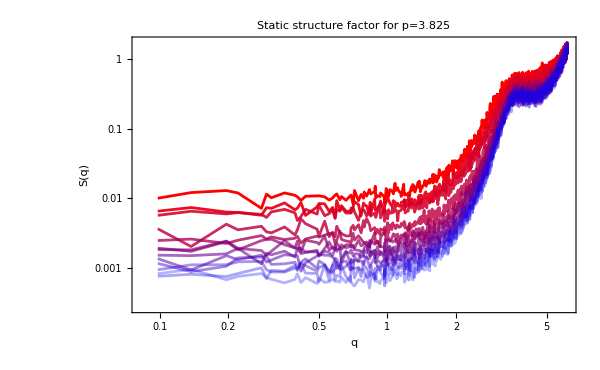
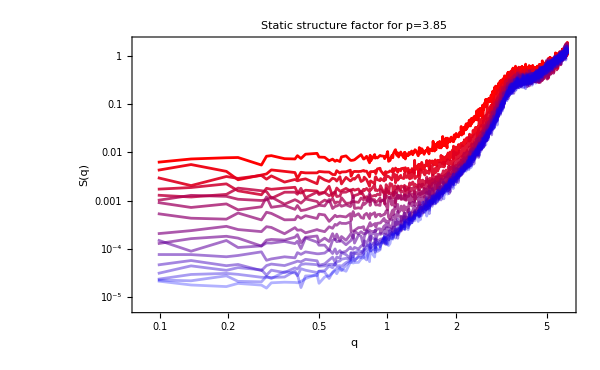
```mathematica
sq={-Graphics-,-Graphics-,-Graphics-};
```

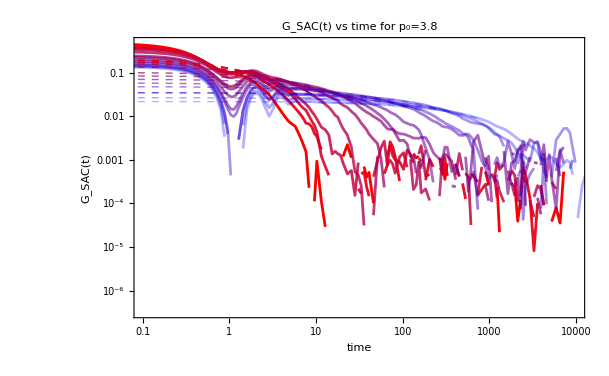
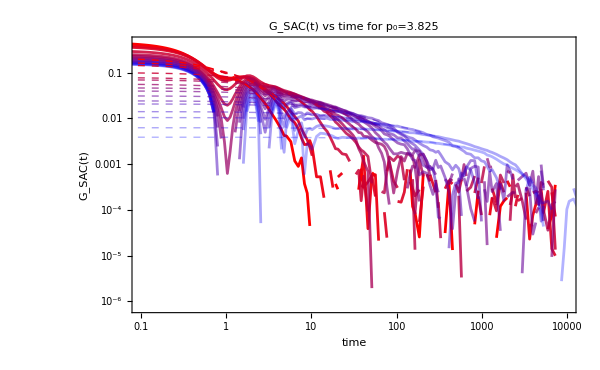
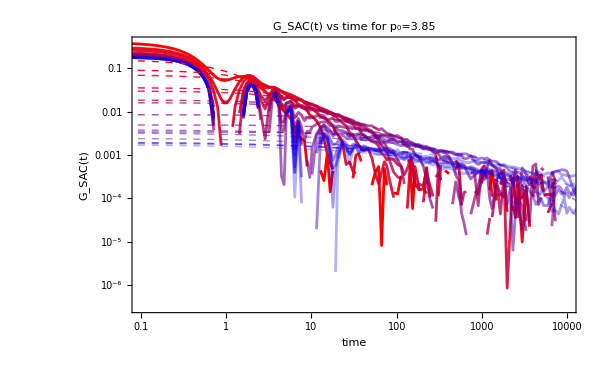
```mathematica
gt={-Graphics-,-Graphics-,-Graphics-};
```

```mathematica
Export["/home/chengling/Research/updates/07142024/sqandGt.jpeg",Grid[Partition[Flatten[Table[{sq[[p]],gt[[p]]},{p,Length[p0s]}]],2]],ImageResolution->400]
```

/home/chengling/Research/updates/07142024/sqandGt.jpeg